```mathematica
SetDirectory[NotebookDirectory[]];
<< Italy2018ElectionDataAnalysis.wl;
```

```mathematica
PieChart[PlottingElectionElectorsPie["CAMERA", region-> "MOLISE"], ChartLegends->{"Votanti maschi", "Votanti femmine"}]
```

-Graphics-

```mathematica
PieChart[PlottingElectionVotersPie["camera", query->"ELETTORI = 13746"], ChartLegends->{"Votanti maschi", "Votanti femmine"}]
```

-Graphics-

```mathematica
PieChart[PlottingElectionVotersNonVotersPie["camera"], ChartLegends->{"Votanti maschi", "Votanti femmine", "Non votanti maschi", "Non votanti femmine"}]
```

-Graphics-

```mathematica
divisions=EntityValue[Entity["AdministrativeDivision",{EntityProperty["AdministrativeDivision","ParentRegion"]->Entity["Country","Italy"]}],"Entities"];
divisionsVotes = Table[Transpose @ {divisions, PlottingElectionRegionCoalitionsBars["camera", coalition] }, {coalition, {"Sinistra", "Centro", "Destra"}}];
GeoRegionValuePlot[Table[rv, {rv,  divisionsVotes}]]
```

GeoRegionValuePlot::ldata: … is not a valid dataset or list of datasets.

GeoRegionValuePlot[{{{Abruzzes, Italy,567410},{Apulia, Italy,271975},{Basilicata, Italy,683616},{Calabria, Italy,2111329},{Campania, Italy,3265739},{Emilia-Romagna, Italy,677301},{Friuli-Venezia Giulia, Italy,2998477},{Lazio, Italy,882054},{Liguria, Italy,5887437},{Lombardy, Italy,900646},{Marche, Italy,131785},{Molise, Italy,2619753},{Piemonte, Italy,1510688},{Sardegna, Italy,652335},{Sicily, Italy,1410328},{Toscana, Italy,3014009},{Trentino-Alto Adige, Italy,0},{Umbria, Italy,586538},{Valle d'Aosta, Italy,0},{Veneto, Italy,2430617}},{{Abruzzes, Italy,303006},{Apulia, Italy,139158},{Basilicata, Italy,406684},{Calabria, Italy,1490313},{Campania, Italy,704468},{Emilia-Romagna, Italy,169299},{Friuli-Venezia Giulia, Italy,1025578},{Lazio, Italy,259950},{Liguria, Italy,1200482},{Lombardy, Italy,316417},{Marche, Italy,78192},{Molise, Italy,648740},{Piemonte, Italy,984338},{Sardegna, Italy,369196},{Sicily, Italy,1181357},{Toscana, Italy,527013},{Trentino-Alto Adige, Italy,0},{Umbria, Italy,141498},{Valle d'Aosta, Italy,0},{Veneto, Italy,696676}},{{Abruzzes, Italy,1089463},{Apulia, Italy,322011},{Basilicata, Italy,1220949},{Calabria, Italy,3367505},{Campania, Italy,3381482},{Emilia-Romagna, Italy,1197222},{Friuli-Venezia Giulia, Italy,4407349},{Lazio, Italy,1286912},{Liguria, Italy,10552680},{Lombardy, Italy,1184178},{Marche, Italy,208793},{Molise, Italy,4017626},{Piemonte, Italy,2828050},{Sardegna, Italy,1085221},{Sicily, Italy,3075167},{Toscana, Italy,2756419},{Trentino-Alto Adige, Italy,0},{Umbria, Italy,758537},{Valle d'Aosta, Italy,0},{Veneto, Italy,5536512}}}]

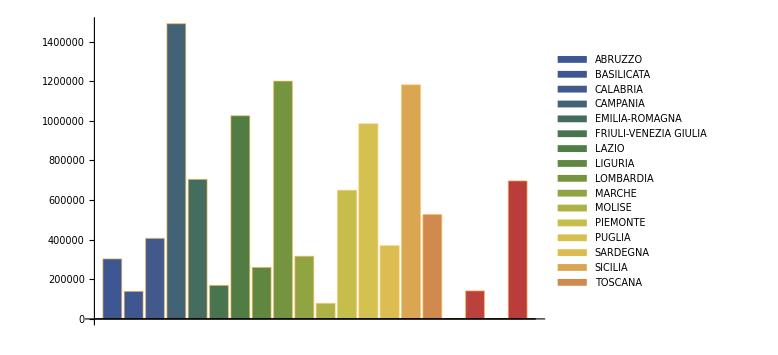

```mathematica
BarChart[PlottingElectionRegionCoalitionsBars["camera", "Centro"], ChartLegends->GetRegions[], ImageSize->Large, ChartStyle->"DarkRainbow"]
```

```mathematica
luigidimaio=PlottingCandidate["luigi", "di maio",city->"pomigliano d'arco"]
```

{03 - ACERRA,,,}

```mathematica
notfound = PlottingCandidate["tommaso","azzalin"]
```

{NOT FOUND,,,}

```mathematica
"CAMERA" === ToUpperCase["camera"]
```

True

{03 - ACERRA,,,}

{NOT FOUND,,,}

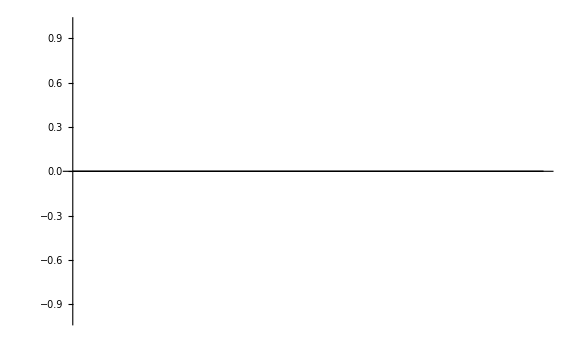

```mathematica
BarChart[notfound[[4]],ChartLegends->notfound[[2]],ImageSize->Large,ChartStyle->"DarkRainbow"]
```

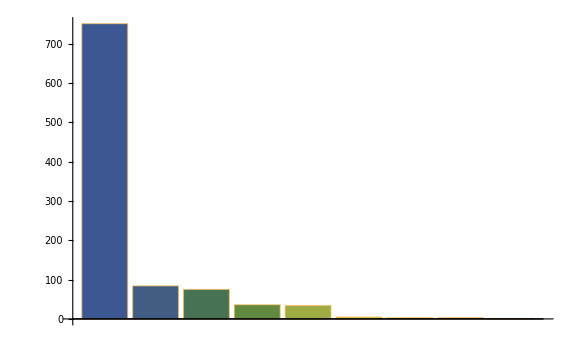

```mathematica
BarChart[luigidimaio[[4]],ChartLegends->luigidimaio[[2]],ImageSize->Large,ChartStyle->"DarkRainbow"]
```